```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={θ<π/2, θ>-π/2,d>0,ϵ>0};
```

```mathematica
df[ζ_]=k(ζ+1)^(θ/π)/ζ;
```

```mathematica
f[ζ_]=∫df[ζ]ⅆζ+c//FullSimplify
```

c+(k π (1+ζ)^((π+θ)/π) Hypergeometric2F1[1,1,1-θ/π,-1/ζ])/(ζ θ)

```mathematica
Limit[f[-1+ϵ ⅈ],ϵ->0,Direction->-1]
```

c+ⅇ^(ⅈ θ) k π Csc[θ]

```mathematica
c=-ⅇ^(ⅈ θ) k π Csc[θ];
```

```mathematica
f[ζ_]=k(-ⅇ^(ⅈ θ)  π Csc[θ]+ π/θ (1+ζ)^((π+θ)/π)/ζ Hypergeometric2F1[1,1,1-θ/π,-1/ζ]);
```

```mathematica
For f[ξ>0] we find that the second term is real. Thus
```

```mathematica
k = ⅈ κ;
```

```mathematica
f[1]- ⅈ κ(- ⅇ^(ⅈ θ) π  Csc[θ]+   (2^((π+θ)/π) π  Hypergeometric2F1[1,1,1-θ/π,-1])/θ)//Simplify
```

0

```mathematica
Re[f[1]]== κ(- Im[ⅇ^(ⅈ θ)] π  Csc[θ])== κ π(-Sin[θ]    Csc[θ])== κ π = L
```

```mathematica
κ=L/π;
```

```mathematica
f[ζ_]=ⅈ L/π(-ⅇ^(ⅈ θ)  π Csc[θ]+ π/θ (1+ζ)^((π+θ)/π)/ζ Hypergeometric2F1[1,1,1-θ/π,-1/ζ]);
```

```mathematica
L=50;
θ = 10*π/180;
```

```mathematica
lim={-2,2,0.001,1};
```

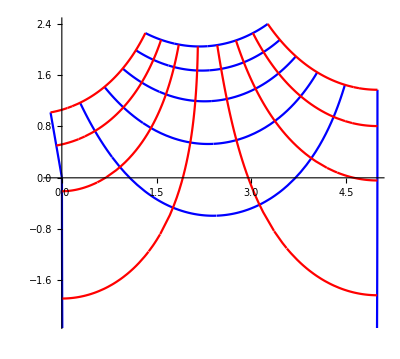

```mathematica
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]
```

```mathematica
g[λ_]:=f[Exp[λ]];
```

```mathematica
lim={-.2,.2,0.001,π};
```

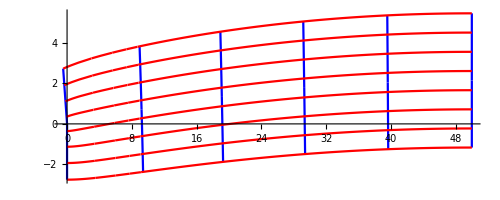

```mathematica
Show[ParametricPlot[Array[ReIm@g[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@g[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]
```